```mathematica
ClearAll["Global`*"]
```

```mathematica
namelist={ToString[Vladimir Putin],ToString[Barack Obama],ToString[Xi Jinping],ToString[Pope Francis],ToString[Angela Merkel],ToString[Bill Gates],ToString[Ben Bernanke],ToString[Abdullah bin Abdul Aziz Al Saud],ToString[Mario Draghi],ToString[Michael Duke],ToString[David Cameron],ToString[Carlos Slim Helu],ToString[Warren Buffett],ToString[Li Keqiang],ToString[Jeff Bezos],ToString[Rex Tillerson],ToString[Sergey Brin],ToString[Larry Page],ToString[Francois Hollande],ToString[Timothy Cook],ToString[Dilma Rousseff],ToString[Sonia Gandhi],ToString[Jamie Dimon],ToString[Ali Hoseini-Khamenei],ToString[Mark Zuckerberg],ToString[Jeffrey Immelt],ToString[Benjamin Netanyahu],ToString[Lloyd Blankfein],ToString[Manmohan Singh],ToString[Michael Bloomberg],ToString[Li Ka-shing],ToString[Charles Koch],ToString[David Koch],ToString[Ban Ki-moon],ToString[Rupert Murdoch],ToString[Khalifa bin Zayed Al-Nahyan],ToString[Christine Lagarde],ToString[Xuedong Ding],ToString[Enrique Pena Nieto],ToString[Mukesh Ambani],ToString[Haruhiko Kuroda],ToString[Ali Al-Naimi],ToString[Lee Kun-Hee],ToString[Larry Fink],ToString[Bill Clinton],ToString[Akio Toyoda],ToString[Masayoshi Son],ToString[Kim Jong-un],ToString[Elon Musk],ToString[Terry Gou],ToString[Martin Winterkorn],ToString[Jim Yong Kim],ToString[Lakshmi Mittal],ToString[Geun-hye Park],ToString[Dmitry Medvedev],ToString[Bernard Arnault], ToString[Bill Gross],ToString[Virginia Rometty],ToString[Shinzo Abe],ToString[Larry Ellison],ToString[Margaret Chan],ToString[Igor Sechin],ToString[Robin Li],ToString[John Roberts],ToString[Alisher Usmanov],ToString[Aliko Dangote],ToString[Reid Hoffman],ToString[John Boehner],ToString[Joaquin Guzman Loera],ToString[Jill Abramson],ToString[Joseph Blatter],ToString[Yngve Slyngstad],ToString[Mohammed Ibrahim],ToString[Janet Yellen]};

Do[
name[n]=namelist[[n]];

F =Import["/Users/danielgladstone/Documents/twitter_project/graph/"<>name[n]];

GList[n]=Table[
joined=First[F[[i]]]->Last[F[[i]]]
,{i,1,Length[F]}];
G=Graph[GList[n]];
VC[n]=VertexCount[G];
VID[n]=Mean[VertexInDegree[G]];
CC[n]=Mean[ClosenessCentrality[G]];
GD[n]=GraphDensity[G];
GR[n]=GraphReciprocity[G];
GCC[n]=GlobalClusteringCoefficient[G];
GA[n]=GraphAssortativity[G];
MND[n]=Mean[MeanNeighborDegree[G]];
MDC[n]=Mean[MeanDegreeConnectivity[G]];

,{n,Length[namelist]}]
```

Import::infer: Cannot infer format of file "Manmohan Singh".

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

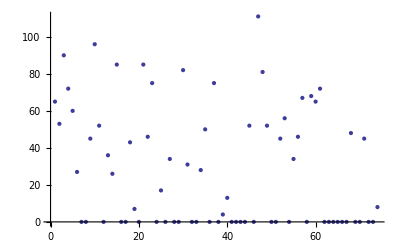

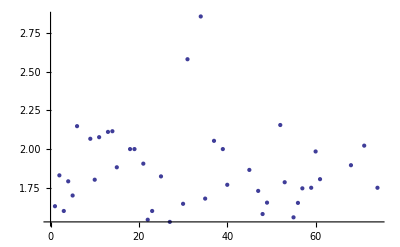

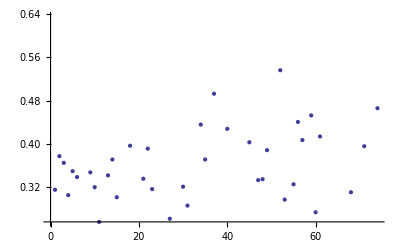

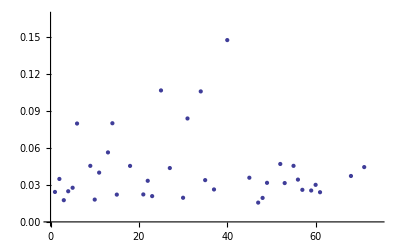

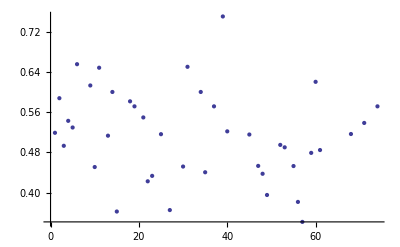

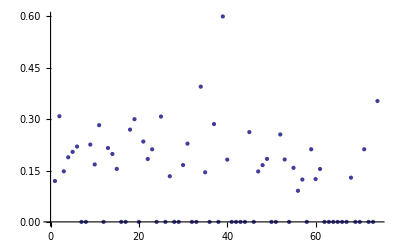

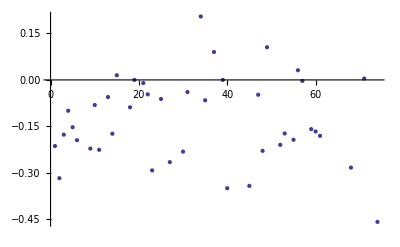

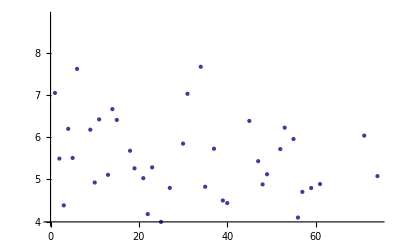

```mathematica
Table[Graph[GList[n]],{n,28}]
ListPlot[Table[VC[j],{j,Length[namelist]}]]
ListPlot[Table[VID[j],{j,Length[namelist]}]]
ListPlot[Table[CC[j],{j,Length[namelist]}]]
ListPlot[Table[GD[j],{j,Length[namelist]}]]
ListPlot[Table[GR[j],{j,Length[namelist]}]]
ListPlot[Table[GCC[j],{j,Length[namelist]}]]
ListPlot[Table[GA[j],{j,Length[namelist]}]]
ListPlot[Table[MND[j],{j,Length[namelist]}]]
ListPlot[Table[MDC[j],{j,Length[namelist]}]]
```

```mathematica
Range[Length[namelist]]
Table[VC[j],{j,Length[namelist]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

{4,13,105,57,95,67,64,68,0,8,79,0}

```mathematica
G=Graph[GList]

VertexCount[G]
Mean[VertexInDegree[G]]
Mean[ClosenessCentrality[G]]
GraphDensity[G]
GraphReciprocity[G]
GlobalClusteringCoefficient[G]
GraphAssortativity[G]
Mean[MeanNeighborDegree[G]]
Mean[MeanDegreeConnectivity[G]]
```

-Graphics-

4

2

0.9375

2/3

3/4

3/5

0

9/2

7/3

```mathematica
First[F[[1]]]->Last[F[[1]]]
```

#cat→#cats

```mathematica
.
```

```mathematica
Table[
Print[i];
,{i,2,5}]
```

2

3

4

5

{Null,Null,Null,Null}